```mathematica
Exp[Dt[f[x]]]
```

ⅇ^(Dt[x] f'[x])

```mathematica
Dt[Exp[f[x]]]
```

ⅇ^f[x] Dt[x] f'[x]

```mathematica
Exp[f[x]] Dt[f[x]]
```

ⅇ^f[x] Dt[x] f'[x]

```mathematica
Sum[2^i x^i,{x,0,10,1}]
```

0^i+2^i+2^(2 i)+6^i+8^i+10^i+12^i+14^i+16^i+18^i+20^i

```mathematica
Sum[2^i x^i,{i,0,10,1}]
```

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10

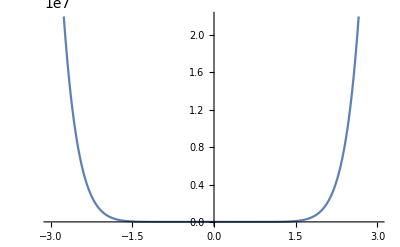

```mathematica
Plot[1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10,{x,-3.,3.}]
```

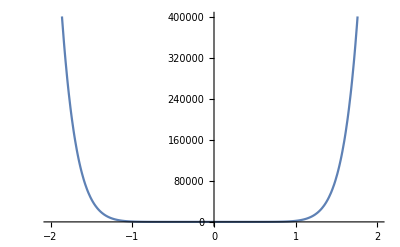

```mathematica
Plot[1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10,{x,-2,2}]
```

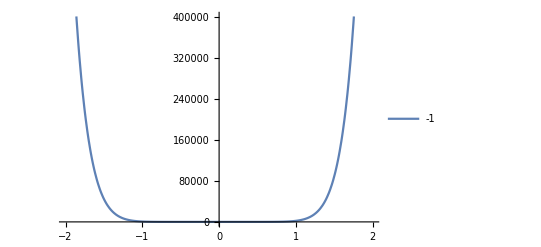

```mathematica
Plot[1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10,{x,-2,2},PlotLegends->{-1,1}]
```

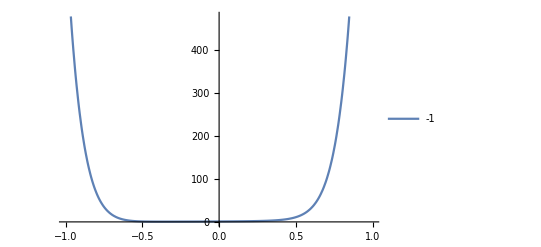

```mathematica
Plot[1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10,{x,-1,1},PlotLegends->{-1,1}]
```

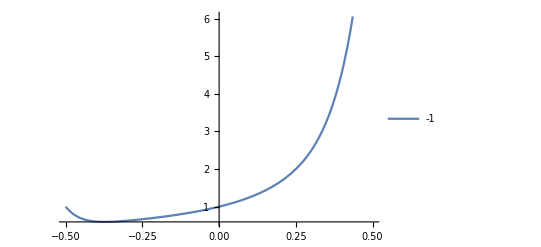

```mathematica
Plot[1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10,{x,-1/2,1/2},PlotLegends->{-1,1}]
```

```mathematica
Manipulate[
Plot[α x^3+β x^2+γ x+η,{x,-3,3}]
,{α,-1,1},{β,-1,1},{γ,-1,1},{η,-1,1}]
```

```mathematica
Manipulate[
Plot[α x^3+β x^2+γ x+η,{x,-3,3}]
,{{α,0},-1,1},{{β,0},-1,1},{{γ,0},-1,1},{{η,0},-1,1}]
```

```mathematica
x^3-x
```

-x+x^3

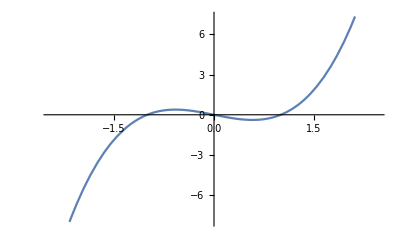

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,-x+x^3}.{1,0}],x∈Reals]
```

1/(√(2-2 x^2+x^4))

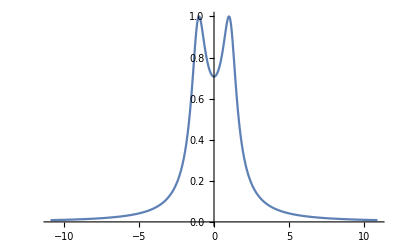

```mathematica
Plot[1/(√(2-2 x^2+x^4)),{x,-10.92,10.92}]
```

```mathematica
D[1/(√(2-2 x^2+x^4)),x]==0
```

-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))==0

```mathematica
Reduce[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))==0]
```

x==-1||x==0||x==1

```mathematica
ExpandAll[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))]
```

(4 x)/(4 √(2-2 x^2+x^4)-4 x^2 √(2-2 x^2+x^4)+2 x^4 √(2-2 x^2+x^4))-(4 x^3)/(4 √(2-2 x^2+x^4)-4 x^2 √(2-2 x^2+x^4)+2 x^4 √(2-2 x^2+x^4))

```mathematica
FullSimplify[Abs[Normalize@{x,f[x]}.{1,0}]==-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2)),{x,f[x]}∈Reals]
```

2 x (-1+x^2)+((2-2 x^2+x^4)^(3/2) Abs[x])/(√(x^2+f[x]^2))==0

```mathematica
Reduce[2 x (-1+x^2)+((2-2 x^2+x^4)^(3/2) Abs[x])/(√(x^2+f[x]^2))==0]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[2 x (-1+x^2)+((2-2 x^2+x^4)^(3/2) Abs[x])/(√(x^2+f[x]^2))==0]

```mathematica
Solve[2 x (-1+x^2)+((2-2 x^2+x^4)^(3/2) Abs[x])/(√(x^2+f[x]^2))==0,f[x]]
```

{{f[x]→-(√(-4 x^4+8 x^6-4 x^8+8 Abs[x]^2-24 x^2 Abs[x]^2+36 x^4 Abs[x]^2-32 x^6 Abs[x]^2+18 x^8 Abs[x]^2-6 x^10 Abs[x]^2+x^12 Abs[x]^2))/(x √(4-8 x^2+4 x^4))},{f[x]→(√(-4 x^4+8 x^6-4 x^8+8 Abs[x]^2-24 x^2 Abs[x]^2+36 x^4 Abs[x]^2-32 x^6 Abs[x]^2+18 x^8 Abs[x]^2-6 x^10 Abs[x]^2+x^12 Abs[x]^2))/(x √(4-8 x^2+4 x^4))}}

```mathematica
FullSimplify[
Solve[
Abs[Normalize@{x,f[x]}.{1,0}]==-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2)),f[x]],{x,f[x]}∈Reals]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→-(√((-2+x^2) (-4+12 x^2-16 x^4+10 x^6-4 x^8+x^10)))/(2 Abs[-1+x^2])},{f[x]→(√((-2+x^2) (-4+12 x^2-16 x^4+10 x^6-4 x^8+x^10)))/(2 Abs[-1+x^2])}}

```mathematica
Table[D[1/(√(1-x^2)),{x,i}],{i,1,10}]
```

{x/((1-x^2)^(3/2)),(3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2)),(15 x^3)/((1-x^2)^(7/2))+(9 x)/((1-x^2)^(5/2)),(105 x^4)/((1-x^2)^(9/2))+(90 x^2)/((1-x^2)^(7/2))+9/((1-x^2)^(5/2)),(945 x^5)/((1-x^2)^(11/2))+(1050 x^3)/((1-x^2)^(9/2))+(225 x)/((1-x^2)^(7/2)),(10395 x^6)/((1-x^2)^(13/2))+(14175 x^4)/((1-x^2)^(11/2))+(4725 x^2)/((1-x^2)^(9/2))+225/((1-x^2)^(7/2)),(135135 x^7)/((1-x^2)^(15/2))+(218295 x^5)/((1-x^2)^(13/2))+(99225 x^3)/((1-x^2)^(11/2))+(11025 x)/((1-x^2)^(9/2)),(2027025 x^8)/((1-x^2)^(17/2))+(3783780 x^6)/((1-x^2)^(15/2))+(2182950 x^4)/((1-x^2)^(13/2))+(396900 x^2)/((1-x^2)^(11/2))+11025/((1-x^2)^(9/2)),(34459425 x^9)/((1-x^2)^(19/2))+(72972900 x^7)/((1-x^2)^(17/2))+(51081030 x^5)/((1-x^2)^(15/2))+(13097700 x^3)/((1-x^2)^(13/2))+(893025 x)/((1-x^2)^(11/2)),(654729075 x^10)/((1-x^2)^(21/2))+(1550674125 x^8)/((1-x^2)^(19/2))+(1277025750 x^6)/((1-x^2)^(17/2))+(425675250 x^4)/((1-x^2)^(15/2))+(49116375 x^2)/((1-x^2)^(13/2))+893025/((1-x^2)^(11/2))}

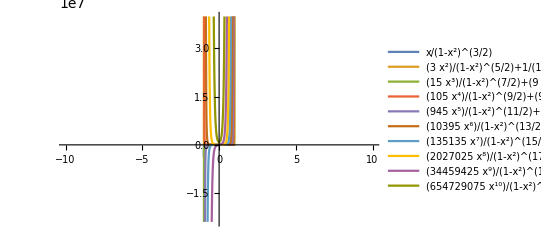

```mathematica
Plot[
{x/((1-x^2)^(3/2)),(3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2)),(15 x^3)/((1-x^2)^(7/2))+(9 x)/((1-x^2)^(5/2)),(105 x^4)/((1-x^2)^(9/2))+(90 x^2)/((1-x^2)^(7/2))+9/((1-x^2)^(5/2)),(945 x^5)/((1-x^2)^(11/2))+(1050 x^3)/((1-x^2)^(9/2))+(225 x)/((1-x^2)^(7/2)),(10395 x^6)/((1-x^2)^(13/2))+(14175 x^4)/((1-x^2)^(11/2))+(4725 x^2)/((1-x^2)^(9/2))+225/((1-x^2)^(7/2)),(135135 x^7)/((1-x^2)^(15/2))+(218295 x^5)/((1-x^2)^(13/2))+(99225 x^3)/((1-x^2)^(11/2))+(11025 x)/((1-x^2)^(9/2)),(2027025 x^8)/((1-x^2)^(17/2))+(3783780 x^6)/((1-x^2)^(15/2))+(2182950 x^4)/((1-x^2)^(13/2))+(396900 x^2)/((1-x^2)^(11/2))+11025/((1-x^2)^(9/2)),(34459425 x^9)/((1-x^2)^(19/2))+(72972900 x^7)/((1-x^2)^(17/2))+(51081030 x^5)/((1-x^2)^(15/2))+(13097700 x^3)/((1-x^2)^(13/2))+(893025 x)/((1-x^2)^(11/2)),(654729075 x^10)/((1-x^2)^(21/2))+(1550674125 x^8)/((1-x^2)^(19/2))+(1277025750 x^6)/((1-x^2)^(17/2))+(425675250 x^4)/((1-x^2)^(15/2))+(49116375 x^2)/((1-x^2)^(13/2))+893025/((1-x^2)^(11/2))}
,{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
Sum[C[i] x^i,{i,1,10}]
```

x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10]

```mathematica
D[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10],x]
```

C[1]+2 x C[2]+3 x^2 C[3]+4 x^3 C[4]+5 x^4 C[5]+6 x^5 C[6]+7 x^6 C[7]+8 x^7 C[8]+9 x^8 C[9]+10 x^9 C[10]

```mathematica
Dt[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10]]
```

C[1] Dt[x]+2 x C[2] Dt[x]+3 x^2 C[3] Dt[x]+4 x^3 C[4] Dt[x]+5 x^4 C[5] Dt[x]+6 x^5 C[6] Dt[x]+7 x^6 C[7] Dt[x]+8 x^7 C[8] Dt[x]+9 x^8 C[9] Dt[x]+10 x^9 C[10] Dt[x]

```mathematica
NestList[Dt,C[1]+2 x C[2]+3 x^2 C[3]+4 x^3 C[4]+5 x^4 C[5]+6 x^5 C[6]+7 x^6 C[7]+8 x^7 C[8]+9 x^8 C[9]+10 x^9 C[10],10]
```

{C[1]+2 x C[2]+3 x^2 C[3]+4 x^3 C[4]+5 x^4 C[5]+6 x^5 C[6]+7 x^6 C[7]+8 x^7 C[8]+9 x^8 C[9]+10 x^9 C[10],9,163296000 C[10] Dt[x]^8 Dt[Dt[x]]+228614400 C[9] Dt[x]^6 Dt[Dt[x]]^2+224+72 x^7 C[9] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]]]+90 x^8 C[10] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]]]}
 |  |  |  |

```mathematica
D[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10],{x,10}]
```

3628800 C[10]

```mathematica
D[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10],{x,11}]
```

0

```mathematica
D[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10],{x,9}]
```

362880 C[9]+3628800 x C[10]

```mathematica
D[x C[1]+x^2 C[2]+x^3 C[3]+x^4 C[4]+x^5 C[5]+x^6 C[6]+x^7 C[7]+x^8 C[8]+x^9 C[9]+x^10 C[10],{x,10}]
```

3628800 C[10]

```mathematica
With[{f={Cos[t],Sin[t]}},
f''.f'
]
```

{Cos[t],Sin[t]}''.{Cos[t],Sin[t]}'

```mathematica
With[{f={Cos[t],Sin[t]}},
Normalize@D[f,{t,2}].Normalize@D[f,t]
]
```

0

```mathematica
FullSimplify[Abs[Normalize@{x,x^3-x}.{1,0}],x∈Reals]
```

1/(√(2-2 x^2+x^4))

```mathematica
Plot[1/(√(2-2 x^2+x^4)),{x,-10.92,10.92}]
```

-Graphics-

```mathematica
D[1/(√(2-2 x^2+x^4)),x]
```

-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))

```mathematica
Solve[D[1/(√(2-2 x^2+x^4)),x]==0,x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
FullSimplify[Abs[Normalize@{x,f[x]}.{1,0}==x^3-x],x∈Reals]
```

Abs[x^3==x (1+1/(√(x^2+Abs[f[x]]^2)))]

```mathematica
FullSimplify[Abs[Normalize@{x,f[x]}.{1,0}]==x^3-x,x∈Reals]
```

x^3==x+Abs[x]/(√(x^2+Abs[f[x]]^2))

```mathematica
Reduce[x^3==x+Abs[x]/(√(x^2+Abs[f[x]]^2))]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[x^3==x+Abs[x]/(√(x^2+Abs[f[x]]^2))]

```mathematica
Solve[x^3==x+Abs[x]/(√(x^2+Abs[f[x]]^2)),f[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→-1/2 √(-4 x^2+Abs[x]^2/(1-x)^2+(3 Abs[x]^2)/(1-x)+(4 Abs[x]^2)/x^2+Abs[x]^2/(1+x)^2+(3 Abs[x]^2)/(1+x))},{f[x]→1/2 √(-4 x^2+Abs[x]^2/(1-x)^2+(3 Abs[x]^2)/(1-x)+(4 Abs[x]^2)/x^2+Abs[x]^2/(1+x)^2+(3 Abs[x]^2)/(1+x))}}

```mathematica
Solve[x^3==x+Abs[x]/(√(x^2+(f[x])^2)),f[x]]
```

{{f[x]→-1/2 √(-4 x^2+Abs[x]^2/(1-x)^2+(3 Abs[x]^2)/(1-x)+(4 Abs[x]^2)/x^2+Abs[x]^2/(1+x)^2+(3 Abs[x]^2)/(1+x))},{f[x]→1/2 √(-4 x^2+Abs[x]^2/(1-x)^2+(3 Abs[x]^2)/(1-x)+(4 Abs[x]^2)/x^2+Abs[x]^2/(1+x)^2+(3 Abs[x]^2)/(1+x))}}

```mathematica
FullSimplify[1/2 √(-4 x^2+Abs[x]^2/(1-x)^2+(3 Abs[x]^2)/(1-x)+(4 Abs[x]^2)/x^2+Abs[x]^2/(1+x)^2+(3 Abs[x]^2)/(1+x)),x∈Reals]
```

√((1-(x-x^3)^2)/((-1+x^2)^2))

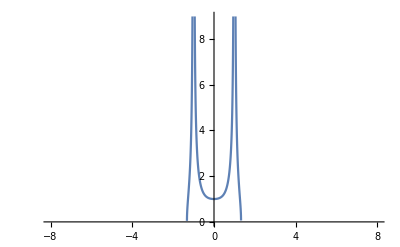

```mathematica
Plot[√((1-(x-x^3)^2)/((-1+x^2)^2)),{x,-8,8}]
```

```mathematica
ExpandAll@√((1-(x-x^3)^2)/((-1+x^2)^2))
```

√(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4))

```mathematica
Plot[√(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)),{x,-8,8}]
```

-Graphics-

```mathematica
D[√(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)),x]
```

(-(-4 x+4 x^3)/((1-2 x^2+x^4)^2)+(x^2 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)-(2 x^4 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)+(x^6 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)-(2 x)/(1-2 x^2+x^4)+(8 x^3)/(1-2 x^2+x^4)-(6 x^5)/(1-2 x^2+x^4))/(2 √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))

```mathematica
ExpandAll@((-(-4 x+4 x^3)/((1-2 x^2+x^4)^2)+(x^2 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)-(2 x^4 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)+(x^6 (-4 x+4 x^3))/((1-2 x^2+x^4)^2)-(2 x)/(1-2 x^2+x^4)+(8 x^3)/(1-2 x^2+x^4)-(6 x^5)/(1-2 x^2+x^4))/(2 √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4))))
```

-x/((1-2 x^2+x^4) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))+(4 x^3)/((1-2 x^2+x^4) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))-(3 x^5)/((1-2 x^2+x^4) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))+(2 x)/((1-4 x^2+6 x^4-4 x^6+x^8) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))-(4 x^3)/((1-4 x^2+6 x^4-4 x^6+x^8) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))+(6 x^5)/((1-4 x^2+6 x^4-4 x^6+x^8) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))-(6 x^7)/((1-4 x^2+6 x^4-4 x^6+x^8) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))+(2 x^9)/((1-4 x^2+6 x^4-4 x^6+x^8) √(1/(1-2 x^2+x^4)-x^2/(1-2 x^2+x^4)+(2 x^4)/(1-2 x^2+x^4)-x^6/(1-2 x^2+x^4)))

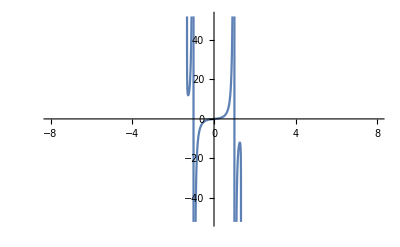

```mathematica
Plot[%50,{x,-8,8}]
```

```mathematica
x^2+y^2==1
```

x^2+y^2==1

```mathematica
FindInstance[x^2+y^2==1,{x,y}]
```

{{x→-1,y→0}}

```mathematica
Dt[x^2+y^2==1]
```

2 x Dt[x]+2 y Dt[y]==0

```mathematica
Solve[2 x Dt[x]+2 y Dt[y]==0,Dt[x]]
```

{{Dt[x]→-(y Dt[y])/x}}

```mathematica
Solve[2 x Dt[x]+2 y Dt[y]==0,Dt[y]]
```

{{Dt[y]→-(x Dt[x])/y}}

```mathematica
Solve[2 x Dt[x]+2 y Dt[y]==0,Dt[y]/Dt[x]]
```

Solve::ivar: Dt[y]/Dt[x] is not a valid variable.

Solve[2 x Dt[x]+2 y Dt[y]==0,Dt[y]/Dt[x]]

```mathematica
∫_0^a x^n ⅆx
```

ConditionalExpression[a^(1+n)/(1+n),Re[n]>-1]

```mathematica
Re[2]+Im[4]
```

2

```mathematica
Re[2]+Im[4+3ⅈ]
```

5

```mathematica
Exp[I π]
```

-1

```mathematica
Exp[2 I π]
```

1

```mathematica
Exp[I π/2]
```

ⅈ

```mathematica
Exp[Exp[I π/2] π]
```

-1

```mathematica
Exp[(π Exp[I π/2])/2]
```

ⅈ

```mathematica
Exp[π Exp[I π/2] ]
```

-1

```mathematica
Exp[2π Exp[I π/2] ]
```

1

```mathematica
Exp[I π]
```

-1

```mathematica
Exp[I π] ==Exp[Exp[I π/2]  Pi/2]
```

False

```mathematica
Exp[I π]
```

-1

```mathematica
Exp[Exp[I π/2]  Pi/2]
```

ⅈ

```mathematica
Exp[I π/2]
```

ⅈ

```mathematica
Exp[Exp[I π/2] π/2]
```

ⅈ

```mathematica
Exp[Exp[Exp[I π/2] π/2] π/2]
```

ⅈ

```mathematica
CountryData["MiddleEast"]
```

{Bahrain,Cyprus,Egypt,Gaza Strip,Iran,Iraq,Israel,Jordan,Kuwait,Lebanon,Oman,Qatar,Saudi Arabia,Syria,Turkey,United Arab Emirates,West Bank,Yemen}

```mathematica
Map[#->CountryData[#,"GDP"]&,CountryData["MiddleEast"]]
```

{Bahrain→3.21791×10^10 $,Cyprus→2.0047×10^10 $,Egypt→3.32791×10^11 $,Gaza Strip→7.68×10^8 $,Iran→4.18977×10^11 $,Iraq→1.71489×10^11 $,Israel→2.96075×10^11 $,Jordan→3.86547×10^10 $,Kuwait→1.10876×10^11 $,Lebanon→4.95988×10^10 $,Oman→6.62934×10^10 $,Qatar→1.52452×10^11 $,Saudi Arabia→6.46438×10^11 $,Syria→4.0405×10^10 $,Turkey→8.63712×10^11 $,United Arab Emirates→3.48743×10^11 $,West Bank→1.33971×10^10 $,Yemen→3.59545×10^10 $}

```mathematica
Grid@
ReverseSortBy[
Map[#->CountryData[#,"GDP"]&,CountryData["MiddleEast"]]
,Last]
```

Grid[{Turkey→8.63712×10^11 $,Saudi Arabia→6.46438×10^11 $,Iran→4.18977×10^11 $,United Arab Emirates→3.48743×10^11 $,Egypt→3.32791×10^11 $,Israel→2.96075×10^11 $,Iraq→1.71489×10^11 $,Qatar→1.52452×10^11 $,Kuwait→1.10876×10^11 $,Oman→6.62934×10^10 $,Lebanon→4.95988×10^10 $,Syria→4.0405×10^10 $,Jordan→3.86547×10^10 $,Yemen→3.59545×10^10 $,Bahrain→3.21791×10^10 $,Cyprus→2.0047×10^10 $,West Bank→1.33971×10^10 $,Gaza Strip→7.68×10^8 $}]

```mathematica
Grid@
ReverseSortBy[
Map[{#,CountryData[#,"GDP"]}&,CountryData["MiddleEast"]]
,Last]
```

Turkey | 8.63712×10^11 $
Saudi Arabia | 6.46438×10^11 $
Iran | 4.18977×10^11 $
United Arab Emirates | 3.48743×10^11 $
Egypt | 3.32791×10^11 $
Israel | 2.96075×10^11 $
Iraq | 1.71489×10^11 $
Qatar | 1.52452×10^11 $
Kuwait | 1.10876×10^11 $
Oman | 6.62934×10^10 $
Lebanon | 4.95988×10^10 $
Syria | 4.0405×10^10 $
Jordan | 3.86547×10^10 $
Yemen | 3.59545×10^10 $
Bahrain | 3.21791×10^10 $
Cyprus | 2.0047×10^10 $
West Bank | 1.33971×10^10 $
Gaza Strip | 7.68×10^8 $

```mathematica
LinguisticAssistant
```

```mathematica
ComplexPlot[Exp[z π/2],{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z π],{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z π],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[z,{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[z z z,{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[z^3+z^2,{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Zeta[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[z^3+z^2,{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
x x x+ x x
```

x^2+x^3

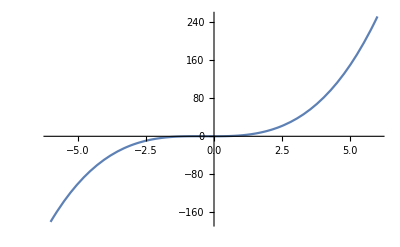

```mathematica
Plot[x^2+x^3,{x,-6.,6.}]
```

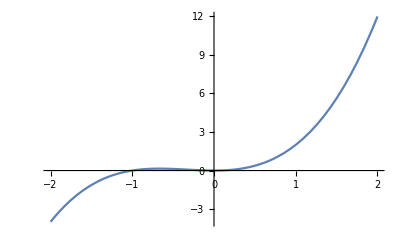

```mathematica
Plot[x^2+x^3,{x,-2,2}]
```

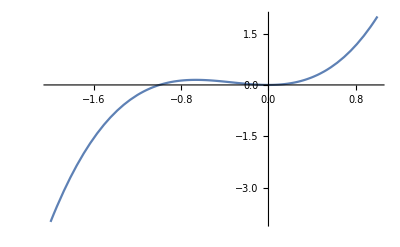

```mathematica
Plot[x^2+x^3,{x,-2,1}]
```

```mathematica
{1,f'[x]}-{x,f[x]}
```

{1-x,-f[x]+f'[x]}

```mathematica
D[{1,3 x^2}-{x,f[x]},f[x]]
```

{0,-1}

```mathematica
D[{1,3 x^2}-{x,f[x]},f[x]]-D[D[{1,3 x^2}-{x,f[x]},f'[x]],x]==0
```

{0,-1}==0

```mathematica
ComplexPlot[Sin[z]+I Cos[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[I Cos[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Cos[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z^2],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[z^2,{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z^3],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z^4],{z,-4-4I,4+4I}]
```

General::munfl: 9.72376×10^-81 3.50033×10^-298 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.72376×10^-81 2.79537×10^-286 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.72376×10^-81 1.83023×10^-274 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
ComplexPlot[Exp[z^5],{z,-4-4I,4+4I}]
```

General::munfl: 3.14159/(1.12945291835652×10^827) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
ComplexPlot[Exp[z^3]Exp[z^2],{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z^3]Exp[z^2 π],{z,-4-4I,4+4I}]
```

-Graphics-